```mathematica
(*Ojo puede que hayamos colocado al revés el modulador y por eso los resultados me dan más parecidos con -ω que con ω, aunque de todos modos no dan iguales.*)
```

Grado de Avance

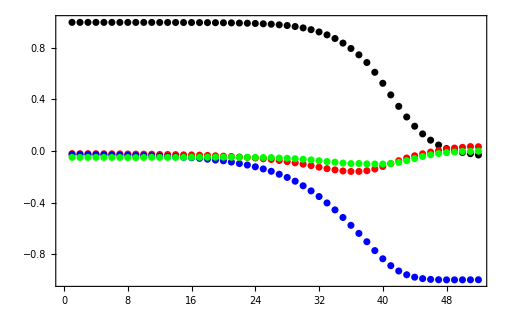

```mathematica
SetDirectory["C:\\Users\\djwiser\\Documents\\Alberto\\Docs\\InfoGral\\SLM\\2011\\de Ciro\\Albertociro5"];
str1="prueba";
Do[name=StringJoin[str1,ToString[i]];
pru[i]=Import[name,"Table"],{i,26}];
m1e=Table[(pru[1][[i+1,1]])/(pru[1][[i+1,1]]+pru[2][[i+1,1]]),{i,52}];(*H/H*)(*entrada/salida*)
m2e=Table[(pru[2][[i+1,1]])/(pru[1][[i+1,1]]+pru[2][[i+1,1]]),{i,52}];(*H/V*)
m3e=Table[(pru[3][[i+1,1]])/(pru[3][[i+1,1]]+pru[4][[i+1,1]]),{i,52}];(*R/V*)
m4e=Table[(pru[4][[i+1,1]])/(pru[3][[i+1,1]]+pru[4][[i+1,1]]),{i,52}];(*R/H*)
m5e=Table[(pru[5][[i+1,1]])/(pru[5][[i+1,1]]+pru[6][[i+1,1]]),{i,52}];(*+45/H*)
m6e=Table[(pru[6][[i+1,1]])/(pru[5][[i+1,1]]+pru[6][[i+1,1]]),{i,52}];(*+45/V*)
m7e=Table[(pru[7][[i+1,1]])/(pru[7][[i+1,1]]+pru[8][[i+1,1]]),{i,52}];(*H/+30*)
m8e=Table[(pru[8][[i+1,1]])/(pru[7][[i+1,1]]+pru[8][[i+1,1]]),{i,52}];(*H/-60*)
m9e=Table[(pru[9][[i+1,1]])/(pru[9][[i+1,1]]+pru[10][[i+1,1]]),{i,52}];(*+45/R*)
m10e=Table[(pru[10][[i+1,1]])/(pru[9][[i+1,1]]+pru[10][[i+1,1]]),{i,52}];(*+45/L*)
m11e=Table[(pru[11][[i+1,1]])/(pru[11][[i+1,1]]+pru[12][[i+1,1]]),{i,52}];(*H/R*)
m12e=Table[(pru[12][[i+1,1]])/(pru[11][[i+1,1]]+pru[12][[i+1,1]]),{i,52}];(*H/L*)
m13e=Table[(pru[13][[i+1,1]])/(pru[13][[i+1,1]]+pru[14][[i+1,1]]),{i,52}];(*V/ *)
m14e=Table[(pru[14][[i+1,1]])/(pru[13][[i+1,1]]+pru[14][[i+1,1]]),{i,52}];(*V/ *)
m15e=Table[(pru[15][[i+1,1]])/(pru[15][[i+1,1]]+pru[16][[i+1,1]]),{i,52}];(*V/ *)
m16e=Table[(pru[16][[i+1,1]])/(pru[15][[i+1,1]]+pru[16][[i+1,1]]),{i,52}]; (*V/*)
m17e=Table[(pru[17][[i+1,1]])/(pru[17][[i+1,1]]+pru[18][[i+1,1]]),{i,52}];(*R/+36*)
m18e=Table[(pru[18][[i+1,1]])/(pru[17][[i+1,1]]+pru[18][[i+1,1]]),{i,52}];(*R/-54*)
m19e=Table[(pru[19][[i+1,1]])/(pru[19][[i+1,1]]+pru[20][[i+1,1]]),{i,52}];(* /+45*)
m20e=Table[(pru[20][[i+1,1]])/(pru[19][[i+1,1]]+pru[20][[i+1,1]]),{i,52}];(* /-45*)
m21e=Table[(pru[21][[i+1,1]])/(pru[21][[i+1,1]]+pru[22][[i+1,1]]),{i,52}];(*H/+45*)
m22e=Table[(pru[22][[i+1,1]])/(pru[21][[i+1,1]]+pru[22][[i+1,1]]),{i,52}];(*H/-45*)
m23e=Table[(pru[23][[i+1,1]])/(pru[23][[i+1,1]]+pru[24][[i+1,1]]),{i,52}];(*+30/R*)
m24e=Table[(pru[24][[i+1,1]])/(pru[23][[i+1,1]]+pru[24][[i+1,1]]),{i,52}];(*+30/L*)
m25e=Table[(pru[25][[i+1,1]])/(pru[25][[i+1,1]]+pru[26][[i+1,1]]),{i,52}];(*+20/L*)
m26e=Table[(pru[26][[i+1,1]])/(pru[25][[i+1,1]]+pru[26][[i+1,1]]),{i,52}];(*+20/R*)          
      
(*Defino la matriz del modulador*)
SLM[X_,Y_,Z_,W_]=({{X-ⅈ Y, Z-ⅈ W}, {-Z-ⅈ W, X+ⅈ Y}});
SLMdag[X_,Y_,Z_,W_]=({{X+ⅈ Y, -Z+ⅈ W}, {Z+ⅈ W, X-ⅈ Y}});
(*Defino el estado de entrada*)
in[θ1_,ϕ1_]={Cos[θ1],Sin[θ1]Exp[ⅈ ϕ1]};
indag[θ1_,ϕ1_]={Cos[θ1],Sin[θ1]Exp[-ⅈ ϕ1]};
(*Defino el estado de salida*)
out[θ2_,ϕ2_]={Cos[θ2],Sin[θ2]Exp[ⅈ ϕ2]};
outdag[θ2_,ϕ2_]={Cos[θ2],Sin[θ2]Exp[-ⅈ ϕ2]};
(*Defino lo que se mide*)
me[θ2_,ϕ2_,X_,Y_,Z_,W_,θ1_,ϕ1_]=Module[{uu},X/:Im[X]=0;X/:Re[X]=X;Y/:Im[Y]=0;Y/:Re[Y]=Y;Z/:Im[Z]=0;Z/:Re[Z]=Z;W/:Im[W]=0;W/:Re[W]=W;uu=indag[θ1,ϕ1].SLMdag[X,Y,Z,W].out[θ2,ϕ2]outdag[θ2,ϕ2].SLM[X,Y,Z,W].in[θ1,ϕ1];(*Re[uu]*)uu];
(*1) H/H*)
m1=Simplify[me[0,0,X,Y,Z,W,0,0]];
(*2) H/V*)
m2=Simplify[me[π/2,0,X,Y,Z,W,0,0]];
(*3) R/V*)
m3=Simplify[me[π/2,0,X,Y,Z,W,π/4,π/2],X^2+Y^2+Z^2+W^2==1];
(*4) R/H*)
m4=Simplify[me[0,0,X,Y,Z,W,π/4,π/2],X^2+Y^2+Z^2+W^2==1];
(*5) +45/H*)
m5=Simplify[me[0,0,X,Y,Z,W,π/4,0],X^2+Y^2+Z^2+W^2==1];
(*6) +45/V*)
m6=Simplify[me[π/2,0,X,Y,Z,W,π/4,0],X^2+Y^2+Z^2+W^2==1];
(*7) H/+30*)
m7=Simplify[me[π/6,0,X,Y,Z,W,0,0],X^2+Y^2+Z^2+W^2==1];
(*8) H/-60*)
m8=Simplify[me[-2*π/6,0,X,Y,Z,W,0,0],X^2+Y^2+Z^2+W^2==1];
(*9) +45/R*)
m9=Simplify[me[π/4,π/2,X,Y,Z,W,π/4,0],X^2+Y^2+Z^2+W^2==1];
(*10) +45/L*)
m10=Simplify[me[-π/4,π/2,X,Y,Z,W,π/4,0],X^2+Y^2+Z^2+W^2==1];
(*11) H/R*)
m11=Simplify[me[π/4,π/2,X,Y,Z,W,0,0],X^2+Y^2+Z^2+W^2==1];
(*12) H/L*)
m12=Simplify[me[-π/4,π/2,X,Y,Z,W,0,0],X^2+Y^2+Z^2+W^2==1];
(*13) V/ *)
m13=Simplify[me[π/8.,π/2,X,Y,Z,W,π/2,0],X^2+Y^2+Z^2+W^2==1];
(*14) V/   *)
m14=Simplify[me[-3*π/8.,π/2,X,Y,Z,W,π/2,0],X^2+Y^2+Z^2+W^2==1];
(*15) V/ *) 
m15=Simplify[me[π/6,π/2,X,Y,Z,W,π/2,0],X^2+Y^2+Z^2+W^2==1];
(*16) V/  *) 
m16=Simplify[me[-2*π/6,π/2,X,Y,Z,W,π/2,0],X^2+Y^2+Z^2+W^2==1];
(*17)R/+36*) 
m17=Simplify[me[π/5.,0,X,Y,Z,W,π/4,π/2],X^2+Y^2+Z^2+W^2==1];
(*18)R/-54*)
m18=Simplify[me[-3*π/10.,0,X,Y,Z,W,π/4,π/2],X^2+Y^2+Z^2+W^2==1];
(*19) /+45*)
m19=Simplify[me[π/4,0,X,Y,Z,W,π/3,π/2],X^2+Y^2+Z^2+W^2==1];
(*20) /-45*)
m20=Simplify[me[-π/4,0,X,Y,Z,W,π/3,π/2],X^2+Y^2+Z^2+W^2==1];
(*21)H/+45*)  
m21=Simplify[me[π/4,0,X,Y,Z,W,0,0],X^2+Y^2+Z^2+W^2==1];
(*22) H/-45*)
m22=Simplify[me[-π/4,0,X,Y,Z,W,0,0],X^2+Y^2+Z^2+W^2==1];
(*23)+30/R*)
m23=Simplify[me[π/4,π/2,X,Y,Z,W,π/6,0],X^2+Y^2+Z^2+W^2==1];
(*24)30/L*)
m24=Simplify[me[π/4,-π/2,X,Y,Z,W,π/6,0],X^2+Y^2+Z^2+W^2==1];
(*25) +20/L*)
m25=Simplify[me[-π/4,π/2,X,Y,Z,W,π/9.,0],X^2+Y^2+Z^2+W^2==1];  
(*26)+20/R*)
m26=Simplify[me[-π/4,-π/2,X,Y,Z,W,π/9.,0],X^2+Y^2+Z^2+W^2==1];
za=0;
zb=.01;
wa=.49;
wb=.5;
xa=.99;
xb=1;
ya=.0;
yb=.01;
Clear[y];
y=0;
Labeled[ProgressIndicator[Dynamic[y]],"Grado de Avance",Top]
Do[
aux=NMinimize[{(m1-m1e[[g]])^2+(m2-m2e[[g]])^2+(m3-m3e[[g]])^2+(m4-m4e[[g]])^2+(m5-m5e[[g]])^2+(m6-m6e[[g]])^2+(m7-m7e[[g]])^2+(m8-m8e[[g]])^2+(m9-m9e[[g]])^2+(m10-m10e[[g]])^2+(m11-m11e[[g]])^2+(m12-m12e[[g]])^2+(m13-m13e[[g]])^2+(m14-m14e[[g]])^2+(m15-m15e[[g]])^2+(m16-m16e[[g]])^2(*+(m17-m17e[[g]])^2*)+(m18-m18e[[g]])^2+(m19-m19e[[g]])^2+(m20-m20e[[g]])^2+(m21-m21e[[g]])^2+(m22-m22e[[g]])^2+(m23-m23e[[g]])^2+(m24-m24e[[g]])^2+(m25-m25e[[g]])^2+(m26-m26e[[g]])^2,-1<X<1&&-1<Y<1&&-1<Z<1&&-1<W<1&&X^2+Y^2+Z^2+W^2==1},{{X,xa,xb},{Y,ya,yb},{Z,za,zb},{W,wa,wb}},Method->{"NelderMead","ShrinkRatio"->.95,"ContractRatio"->.95,"ReflectRatio"->3.5,"Tolerance"->0.0001}];
(*aux=NMinimize[{(m1-m1e[[g]])^2+(m2-m2e[[g]])^2+(m3-m3e[[g]])^2+(m4-m4e[[g]])^2+(m5-m5e[[g]])^2+(m6-m6e[[g]])^2+(m7-m7e[[g]])^2+(m8-m8e[[g]])^2+(m9-m9e[[g]])^2+(m10-m10e[[g]])^2+(m11-m11e[[g]])^2+(m12-m12e[[g]])^2+(m13-m13e[[g]])^2+(m14-m14e[[g]])^2+(m15-m15e[[g]])^2+(m16-m16e[[g]])^2+(m19-m19e[[g]])^2+(m20-m20e[[g]])^2+(m21-m21e[[g]])^2+(m22-m22e[[g]])^2,-1<X<1&&-1<Y<1&&-1<Z<1&&-1<W<1&&X^2+Y^2+Z^2+W^2==1},{{X,xa,xb},{Y,ya,yb},{Z,za,zb},{W,wa,wb}},Method->{"RandomSearch",Method->"InteriorPoint", "SearchPoints"->10}];*)
xyzw[g,4]=W/.aux[[2,4]];
xyzw[g,1]=X/.aux[[2,1]];
xyzw[g,2]=Y/.aux[[2,2]];
xyzw[g,3]=Z/.aux[[2,3]];
xa=xyzw[g,1]-.03;
xb=xyzw[g,1];
ya=xyzw[g,2]-.03;
yb=xyzw[g,2];
za=xyzw[g,3]-.03;
zb=xyzw[g,3];
wa=xyzw[g,4]-.03;
wb=xyzw[g,4];
y=y+1/52,{g,52}]
XX=Table[xyzw[g,1],{g,52}];
YY=Table[xyzw[g,2],{g,52}];
ZZ=Table[xyzw[g,3],{g,52}];
WW=Table[xyzw[g,4],{g,52}];
ListPlot[{XX,YY,ZZ,WW},PlotRange->{-1.01,1.01},Frame-> True,PlotStyle->{{PointSize[.010],Black},{PointSize[.010],Red},{PointSize[.010],Blue},{PointSize[.010],Green}}]
```

{0.752314,{ϕ1→0.327807,ϕ2→1.14279}}

0.327807

18.782

1.14279

65.4769

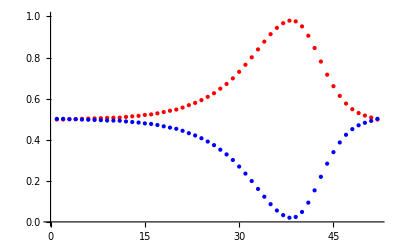

```mathematica
(*Defino la función de intensidad en términos de los niveles de gris para el modulador entre polarizadores con ángulos ϕ1 y ϕ2*)
Int[ϕ1_,ϕ2_,g_]:=(xyzw[g,1] Cos[ϕ1-ϕ2]+xyzw[g,3] Sin[ϕ1-ϕ2])^2+(xyzw[g,2]Cos[ϕ1+ϕ2]+xyzw[g,4]Sin[ϕ1+ϕ2])^2;
(*Modulo que calcula el parametro p*)
p[ϕ1_,ϕ2_]:=Module[{aux,min, max, avg},aux=Table[Int[ϕ1,ϕ2,g],{g,1,52}];
max=Max[aux];
min=Min[aux];
avg=Mean[aux];
Abs[(max-min)/avg]];
aux2=NMinimize[{p[ϕ1,ϕ2],0≤ ϕ1<π&&0≤ ϕ2<π},{ϕ1,ϕ2},MaxIterations->2000,Method->{"NelderMead","ShrinkRatio"->.95,"ContractRatio"->.95,"ReflectRatio"->3.5,"Tolerance"->0.0001}]
(*aux2=NMinimize[{p[ϕ1,ϕ2],0≤ ϕ1<π&&0≤ ϕ2<π},{ϕ1,ϕ2},MaxIterations->2000,Method->{"SimulatedAnnealing","PerturbationScale"->5,"SearchPoints"->100}]*)
(*aux2=NMinimize[{p[ϕ1,ϕ2],0≤ ϕ1<π&&0≤ ϕ2<π},{ϕ1,ϕ2},Method->{"RandomSearch",Method->"InteriorPoint", "SearchPoints"->5}]*)
x=ϕ1/.aux2[[2,1]]
x 180/π
y=ϕ2/.aux2[[2,2]]
y 180/π
aux3=Table[Int[x,y,g],{g,1,52}];
aux5=Table[Int[x,y-π/2,g],{g,1,52}];
ListPlot[{aux3,aux5},PlotRange->{0,1},PlotStyle->{Red,Blue}]
```

```mathematica
(*Una vez medida la fase con los polarizadores en los ángulos predichos anteriormente, importo los datos. Los datos deben estar en el mismo directorio que el resto*)
faser=(*Module[{aux},aux=Import["fase.dat"];Table[aux[[n,2]],{n,52}]]*){0.0822,0.1423,0.1907,0.2287,0.2573,0.2777,0.2911,0.2984,0.3007,0.2990,0.2942,0.2872,0.2788,0.2698,0.2610,0.2532,0.2469,0.2429,
0.2417,0.2438,0.2499,0.2603,0.2755,0.2959,0.3218,0.3535,0.3913,0.4354,0.4860,0.5432,0.6071,0.6778,0.7552,0.8394,0.9302,1.0276,1.1314,
1.2414,1.3573,1.4788,1.6058,1.7377,1.8741,2.0147,2.1589,2.3062,2.4560,2.6077,2.7607,2.9142,3.0674,3.2197};
(*Defino la fase global como la fase total medida menos la fase de la matriz. ang1 y ang2 son los ángulos hallados por el programa da minimización y empleados para medir las fases*)
ang1=127.6;
ang2=173.9;
β=Table[ -faser[[g]]-ArcTan[(xyzw[g,2]Cos[(ang1+ang2)π/180]+xyzw[g,4] Sin[(ang1+ang2)π/180])/(xyzw[g,1]Cos[(ang1-ang2)π/180]+xyzw[g,3] Sin[(ang1-ang2)π/180])],{g,52}];
```

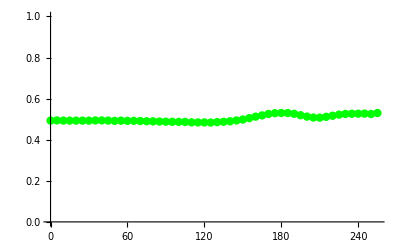

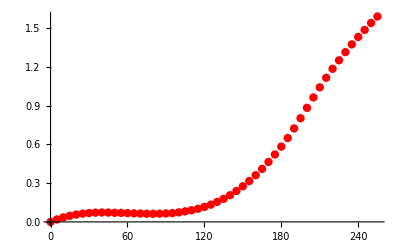

Máxima variación de fase = 1.59058

Angulo del polarizador = 77.8281

Angulo del analizador = 167.489

Angulo de la lámina = 131.854

```mathematica
(*Defino la lámina de cuarto de onda*)
qwp[θ_]={{Cos[θ]^2+I Sin[θ]^2,(1-I)Cos[θ]Sin[θ]},{(1-I)Cos[θ]Sin[θ],I Cos[θ]^2+Sin[θ]^2}};
qwpdag[θ_]={{Cos[θ]^2-I Sin[θ]^2,(1+I)Cos[θ]Sin[θ]},{(1+I)Cos[θ]Sin[θ],-I Cos[θ]^2+Sin[θ]^2}};

(*Como existen, en pricipio, tres posibilidades: lámina antes, lámina después y sin lámina, se analizan todas.*)

(*Defino la intensidad con lámina antes del modulador*)
mepla[θ2_,ϕ2_,X_,Y_,Z_,W_,θ1_,ϕ1_,ω_]=Module[{uu},X/:Im[X]=0;X/:Re[X]=X;Y/:Im[Y]=0;Y/:Re[Y]=Y;Z/:Im[Z]=0;Z/:Re[Z]=Z;W/:Im[W]=0;W/:Re[W]=W;uu=indag[θ1,ϕ1].qwpdag[ω].SLMdag[X,Y,Z,W].out[θ2,ϕ2]outdag[θ2,ϕ2].SLM[X,Y,Z,W].qwp[ω].in[θ1,ϕ1];Re[uu]];

(*Defino la fase de la matriz con la lámina al principio*)fasexyzw[θ2_,X_,Y_,Z_,W_,θ1_,ω_]=Module[{uu},X/:Im[X]=0;X/:Re[X]=X;Y/:Im[Y]=0;Y/:Re[Y]=Y;Z/:Im[Z]=0;Z/:Re[Z]=Z;W/:Im[W]=0;W/:Re[W]=W;uu=outdag[θ2,0].SLM[X,Y,Z,W].qwp[ω].in[θ1,0];Arg[uu]];

(*Defino la fase total*)
fasepla[θ2_,θ1_,ω_,g_]:=-β[[g]]+fasexyzw[θ2,xyzw[g,1],xyzw[g,2],xyzw[g,3],xyzw[g,4],θ1,ω];

(*Defino el parámetro p con lámina siguiendo la definición de la JAP*)
ppla[θ1_,θ2_,ω_]:=Module[{aux,min, max, avg},aux=Table[mepla[θ2,0,xyzw[g,1],xyzw[g,2],xyzw[g,3],xyzw[g,4],θ1,0,ω],{g,52}];
max=Max[aux];
min=Min[aux];
avg=Mean[aux];
(max-min)/avg];

(*Defino una función a Maximizar que me sirva para la búsqueda de la mayor variación de fase*)
qq1[θ2_,θ1_,ω_]:=Module[{min, max,q},q=Table[Mod[(fasepla[θ2,θ1,ω,g]-fasepla[θ2,θ1,ω,52])/π,1],{g,52}];
min=Min[q];
max=Max[q];
max-min]

(*Busco las combinaciones de ángulos que minimizan el cociente entre ppla y qq1. Los parámetros a y b permiten variar los pesos relativos de cada uno en el proceso de minimización*)
a=1;
b=1;
auxmaxfase1=NMinimize[{Abs[ppla[ϕ1,ϕ2,ω]^a/qq1[ϕ2,ϕ1,ω]^b],0≤ ϕ1≤π,0≤ ϕ2≤π,0≤ ω≤π},{ϕ1,ϕ2,ω},MaxIterations->2000,Method->{"NelderMead","ShrinkRatio"->.95,"ContractRatio"->.95,"ReflectRatio"->1.1,"Tolerance"->0.0001}];
(*Recupero los valores que minimizan y grafico la variación de intensidad y fase predicha por el modelo. Muestro además los valores de los ángulos obtenidos*)
ϕϕ1max1=ϕ1/.auxmaxfase1[[2,1]];
ϕϕ2max1=ϕ2/.auxmaxfase1[[2,2]];
ωωmax1=ω/.auxmaxfase1[[2,3]];
intpla2max1=Table[{(g-1)5,mepla[ϕϕ2max1,0,xyzw[g,1],xyzw[g,2],xyzw[g,3],xyzw[g,4],ϕϕ1max1,0,ωωmax1]},{g,52}];
ListPlot[intpla2max1,PlotRange->{0,1},PlotStyle->{Green,PointSize[0.015]}]
fasemax2max1=Table[{(g-1)5,Mod[(fasepla[ϕϕ2max1,ϕϕ1max1,ωωmax1,g]-fasepla[ϕϕ2max1,ϕϕ1max1,ωωmax1,1])/π,2]},{g,52}];
ListPlot[fasemax2max1,PlotRange->All,PlotStyle->{Red,PointSize[0.015]}]
Print[StringJoin["Máxima variación de fase = ",ToString[(Max[Take[fasemax2max1,All,{2}]]-Min[Take[fasemax2max1,All,{2}]])]]];
Print[StringJoin["Angulo del polarizador = ",ToString[ϕϕ1max1 180/π]]];
Print[StringJoin["Angulo del analizador = ",ToString[ϕϕ2max1 180/π]]];
Print[StringJoin["Angulo de la lámina = ",ToString[ωωmax1 180/π]]];
```

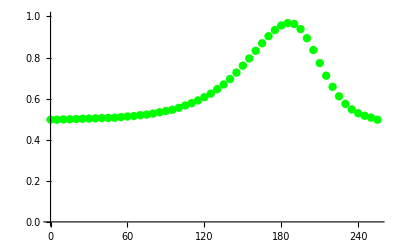

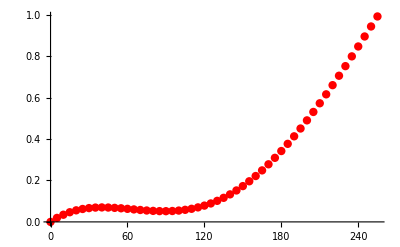

Máxima variación de fase = 0.992105

Angulo del polarizador = 133.384

Angulo del analizador = 0.

Angulo de la lámina = 180.

```mathematica
(*Defino lo que se mide con lámina después del modulador*)
mepla2[θ2_,ϕ2_,X_,Y_,Z_,W_,θ1_,ϕ1_,ω_]=Module[{uu},X/:Im[X]=0;X/:Re[X]=X;Y/:Im[Y]=0;Y/:Re[Y]=Y;Z/:Im[Z]=0;Z/:Re[Z]=Z;W/:Im[W]=0;W/:Re[W]=W;uu=indag[θ1,ϕ1].SLMdag[X,Y,Z,W].qwp[ω].out[θ2,ϕ2]outdag[θ2,ϕ2].qwpdag[ω].SLM[X,Y,Z,W].in[θ1,ϕ1];Re[uu]];

(*Defino la fase de la medida con la lámina al final*)fasexyzw2[θ2_,X_,Y_,Z_,W_,θ1_,ω_]=Module[{uu},X/:Im[X]=0;X/:Re[X]=X;Y/:Im[Y]=0;Y/:Re[Y]=Y;Z/:Im[Z]=0;Z/:Re[Z]=Z;W/:Im[W]=0;W/:Re[W]=W;uu=outdag[θ2,0].qwpdag[ω].SLM[X,Y,Z,W].in[θ1,0];Arg[uu]];
(*Defino la fase total*)
fasepla2[θ2_,θ1_,ω_,g_]:=-β[[g]]+fasexyzw2[θ2,xyzw[g,1],xyzw[g,2],xyzw[g,3],xyzw[g,4],θ1,ω];
(*Defino el parámetro p con lámina después del modulador, siguiendo la definición de la JAP*)
ppla2[θ1_,θ2_,ω_]:=Module[{aux,min, max, avg},aux=Table[mepla2[θ2,0,xyzw[g,1],xyzw[g,2],xyzw[g,3],xyzw[g,4],θ1,0,ω],{g,52}];
max=Max[aux];
min=Min[aux];
avg=Mean[aux];
(max-min)/avg];
(*Defino un un parámetro a Maximizar que me sirva para buscar la mayor variación de fase*)
qq2[θ2_,θ1_,ω_]:=Module[{min, max,q},q=Table[Mod[(fasepla2[θ2,θ1,ω,g]-fasepla2[θ2,θ1,ω,1])/π,52],{g,1,52}];
min=Min[q];
max=Max[q];
(max-min)/(2π)]
(*Busco las combinaciones de ángulos que minimizan el cociente entre ppla y qq1. Los parámetros a y b permiten variar los pesos relativos de cada uno en el proceso de minimización*)
a2=1;
b2=1;
auxmaxfase2=NMinimize[{Abs[ppla2[ϕ1,ϕ2,-ω]^a2/qq2[ϕ2,ϕ1,-ω]^b2],0≤ ϕ1≤π,0≤ ϕ2≤π,0≤ ω≤π},{ϕ1,ϕ2,ω},MaxIterations->4000,Method->{"NelderMead","ShrinkRatio"->.99,"ContractRatio"->.4,"ReflectRatio"->5.3,"Tolerance"->0.00001,"RandomSeed"->5}];

(*Recupero los valores que minimizan y grafico la variación de intensidad y fase predicha por el modelo. Muestro además los valores de los ángulos obtenidos*)
ϕϕ1max2=ϕ1/.auxmaxfase2[[2,1]];
ϕϕ2max2=ϕ2/.auxmaxfase2[[2,2]];
ωωmax2=ω/.auxmaxfase2[[2,3]];
intpla2max2=Table[{(g-1)5,mepla2[ϕϕ2max2,0,xyzw[g,1],xyzw[g,2],xyzw[g,3],xyzw[g,4],ϕϕ1max2,0,ωωmax2]},{g,52}];
ListPlot[intpla2max2,PlotRange->{0,1},PlotStyle->{Green,PointSize[0.015]}]
fasemax2max2=Table[{(g-1)5,Mod[(fasepla2[ϕϕ2max2,ϕϕ1max2,ωωmax2,g]-fasepla2[ϕϕ2max2,ϕϕ1max2,ωωmax2,1])/π,2]},{g,1,52}];
ListPlot[fasemax2max2,PlotRange->All,PlotStyle->{Red,PointSize[0.015]}]
Print[StringJoin["Máxima variación de fase = ",ToString[(Max[Take[fasemax2max2,All,{2}]]-Min[Take[fasemax2max2,All,{2}]])]]];
Print[StringJoin["Angulo del polarizador = ",ToString[ϕϕ1max2 180/π]]];
Print[StringJoin["Angulo del analizador = ",ToString[ϕϕ2max2 180/π]]];
Print[StringJoin["Angulo de la lámina = ",ToString[ωωmax2 180/π]]];
```

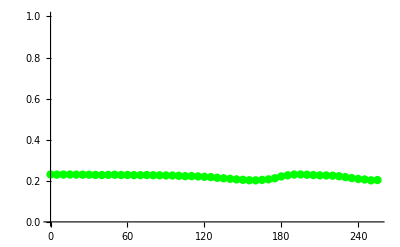

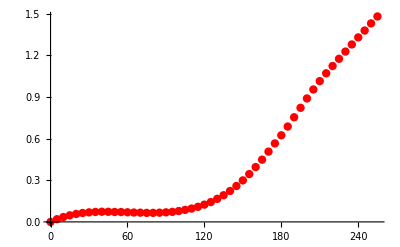

Máxima variación de fase = 1.48139

Angulo del polarizador = 0.602354

Angulo del analizador = 36.2482

Angulo de la lámina = 165.754

Angulo de la lámina = 82.8827

```mathematica
(*Defino lo que se mide con 2 láminas*)
mepla3[θ2_,ϕ2_,X_,Y_,Z_,W_,θ1_,ϕ1_,ω1_,ω2_]=Module[{uu},X/:Im[X]=0;X/:Re[X]=X;Y/:Im[Y]=0;Y/:Re[Y]=Y;Z/:Im[Z]=0;Z/:Re[Z]=Z;W/:Im[W]=0;W/:Re[W]=W;uu=indag[θ1,ϕ1].qwpdag[ω1].SLMdag[X,Y,Z,W].qwp[ω2].out[θ2,ϕ2]outdag[θ2,ϕ2].qwpdag[ω2].SLM[X,Y,Z,W].qwp[ω1].in[θ1,ϕ1];Re[uu]];
(*Defino la fase de la medida con dos láminas*)fasexyzw3[θ2_,X_,Y_,Z_,W_,θ1_,ω1_,ω2_]=Module[{uu},X/:Im[X]=0;X/:Re[X]=X;Y/:Im[Y]=0;Y/:Re[Y]=Y;Z/:Im[Z]=0;Z/:Re[Z]=Z;W/:Im[W]=0;W/:Re[W]=W;uu=outdag[θ2,0].qwpdag[ω2].SLM[X,Y,Z,W].qwp[ω1].in[θ1,0];Arg[uu]];
(*Defino la fase total*)
fasepla3[θ2_,θ1_,ω1_,ω2_,g_]:=-β[[g]]+fasexyzw3[θ2,xyzw[g,1],xyzw[g,2],xyzw[g,3],xyzw[g,4],θ1,ω1,ω2];
(*Defino el parámetro p con lámina después del modulador, siguiendo la definición de la JAP*)
ppla3[θ1_,θ2_,ω1_,ω2_]:=Module[{aux,min, max, avg},aux=Table[mepla3[θ2,0,xyzw[g,1],xyzw[g,2],xyzw[g,3],xyzw[g,4],θ1,0,ω1,ω2],{g,52}];
max=Max[aux];
min=Min[aux];
avg=Mean[aux];
(max-min)/avg];

(*Defino un un parámetro a Maximizar que me sirva para buscar la mayor variación de fase*)
qq3[θ2_,θ1_,ω1_,ω2_]:=Module[{min, max,q},q=Table[Mod[(fasepla3[θ2,θ1,ω1,ω2,g]-fasepla3[θ2,θ1,ω1,ω2,1])/π,2],{g,52}];
min=Min[q];
max=Max[q];
max-min]
(*Busco las combinaciones de ángulos que minimizan el cociente entre ppla y qq1. Los parámetros a y b permiten variar los pesos relativos de cada uno en el proceso de minimización*)
a3=1;
b3=1;
auxmaxfase3=NMinimize[{Abs[ppla3[ϕ1,ϕ2,ω1,ω2]^a3/qq3[ϕ2,ϕ1,ω1,ω2]^b3],0≤ ϕ1≤π,0≤ ϕ2≤π,0≤ ω1≤π,0≤ ω2≤π},{ϕ1,ϕ2,ω1,ω2},MaxIterations->2000,Method->{"NelderMead","ShrinkRatio"->.95,"ContractRatio"->.95,"ReflectRatio"->1.1,"Tolerance"->0.0001}];

(*Recupero los valores que minimizan y grafico la variación de intensidad y fase predicha por el modelo. Muestro además los valores de los ángulos obtenidos*)
ϕϕ1max3=ϕ1/.auxmaxfase3[[2,1]];
ϕϕ2max3=ϕ2/.auxmaxfase3[[2,2]];
ωω1max3=ω1/.auxmaxfase3[[2,3]];
ωω2max3=ω2/.auxmaxfase3[[2,4]];
intpla2max3=Table[{(g-1)5,mepla3[ϕϕ2max3,0,xyzw[g,1],xyzw[g,2],xyzw[g,3],xyzw[g,4],ϕϕ1max3,0,ωω1max3,ωω2max3]},{g,52}];
ListPlot[intpla2max3,PlotRange->{0,1},PlotStyle->{Green,PointSize[0.015]}]
fasemax2max3=Table[{(g-1)5,Mod[(fasepla3[ϕϕ2max3,ϕϕ1max3,ωω1max3,ωω2max3,g]-fasepla3[ϕϕ2max3,ϕϕ1max3,ωω1max3,ωω2max3,1])/π,2]},{g,52}];
ListPlot[fasemax2max3,PlotRange->All,PlotStyle->{Red,PointSize[0.015]}]
Print[StringJoin["Máxima variación de fase = ",ToString[(Max[Take[fasemax2max3,All,{2}]]-Min[Take[fasemax2max3,All,{2}]])]]];
Print[StringJoin["Angulo del polarizador = ",ToString[ϕϕ1max3 180/π]]];
Print[StringJoin["Angulo del analizador = ",ToString[ϕϕ2max3 180/π]]];
Print[StringJoin["Angulo de la lámina = ",ToString[ωω1max3 180/π]]];
Print[StringJoin["Angulo de la lámina = ",ToString[ωω2max3 180/π]]];
```

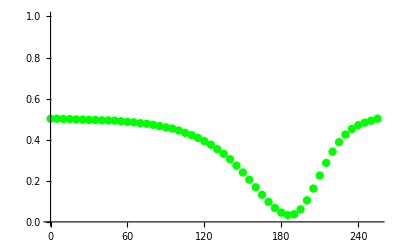

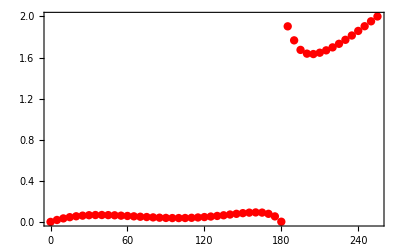

Máxima variación de fase = 1.99999

Angulo del polarizador = 128.312

Angulo del analizador = 84.9462

```mathematica
(*Defino lo que se mide sin láminas*)
mepla4[θ2_,ϕ2_,X_,Y_,Z_,W_,θ1_,ϕ1_]=Module[{uu},X/:Im[X]=0;X/:Re[X]=X;Y/:Im[Y]=0;Y/:Re[Y]=Y;Z/:Im[Z]=0;Z/:Re[Z]=Z;W/:Im[W]=0;W/:Re[W]=W;uu=indag[θ1,ϕ1].SLMdag[X,Y,Z,W].out[θ2,ϕ2]outdag[θ2,ϕ2].SLM[X,Y,Z,W].in[θ1,ϕ1];Re[uu]];
(*Defino la fase de la medida con dos láminas*)fasexyzw4[θ2_,X_,Y_,Z_,W_,θ1_]=Module[{uu},X/:Im[X]=0;X/:Re[X]=X;Y/:Im[Y]=0;Y/:Re[Y]=Y;Z/:Im[Z]=0;Z/:Re[Z]=Z;W/:Im[W]=0;W/:Re[W]=W;uu=outdag[θ2,0].SLM[X,Y,Z,W].in[θ1,0];Arg[uu]];
(*Defino la fase total*)
fasepla4[θ2_,θ1_,g_]:=-β[[g]]+fasexyzw4[θ2,xyzw[g,1],xyzw[g,2],xyzw[g,3],xyzw[g,4],θ1];
(*Defino el parámetro p con lámina después del modulador, siguiendo la definición de la JAP*)
ppla4[θ1_,θ2_]:=Module[{aux,min, max, avg},aux=Table[mepla4[θ2,0,xyzw[g,1],xyzw[g,2],xyzw[g,3],xyzw[g,4],θ1,0],{g,52}];
max=Max[aux];
min=Min[aux];
avg=Mean[aux];
(max-min)/avg];

(*Defino un un parámetro a Maximizar que me sirva para buscar la mayor variación de fase*)
qq4[θ2_,θ1_]:=Module[{min, max,q},q=Table[Mod[(fasepla4[θ2,θ1,g]-fasepla4[θ2,θ1,1])/π,2],{g,2,52}];
min=Min[q];
max=Max[q];
(max-min)/(2π)]

(*Busco las combinaciones de ángulos que minimizan el cociente entre ppla y qq1. Los parámetros a y b permiten variar los pesos relativos de cada uno en el proceso de minimización*)
a4=1;
b4=1;
auxmaxfase4=NMinimize[{Abs[ppla4[ϕ1,ϕ2]^a4/qq4[ϕ2,ϕ1]^b4],0≤ ϕ1≤π&&0≤ ϕ2≤π},{ϕ1,ϕ2},MaxIterations->2000,Method->{"NelderMead","ShrinkRatio"->.95,"ContractRatio"->.95,"ReflectRatio"->1.1,"Tolerance"->0.0001}]

(*Recupero los valores que minimizan y grafico la variación de intensidad y fase predicha por el modelo. Muestro además los valores de los ángulos obtenidos*)
ϕϕ1max4=ϕ1/.auxmaxfase4[[2,1]];
ϕϕ2max4=ϕ2/.auxmaxfase4[[2,2]];
intpla2max4=Table[{(g-1)5,mepla4[ϕϕ2max4,0,xyzw[g,1],xyzw[g,2],xyzw[g,3],xyzw[g,4],ϕϕ1max4,0]},{g,52}];
ListPlot[intpla2max4,PlotRange->{0,1},PlotStyle->{Green,PointSize[0.015]}]
fasemax2max4=Table[{(g-1)5,Mod[(fasepla4[ϕϕ2max4,ϕϕ1max4,g]-fasepla4[ϕϕ2max4,ϕϕ1max4,1])/π,2]},{g,52}];
ListPlot[fasemax2max4,PlotRange->All,PlotStyle->{Red,PointSize[0.015]},Axes->False,Frame->True]
Print[StringJoin["Máxima variación de fase = ",ToString[(Max[Take[fasemax2max4,All,{2}]]-Min[Take[fasemax2max4,All,{2}]])]]];
Print[StringJoin["Angulo del polarizador = ",ToString[ϕϕ1max4 180/π]]];
Print[StringJoin["Angulo del analizador = ",ToString[ϕϕ2max4 180/π]]];
```